```mathematica
(*1 uloha*)
```

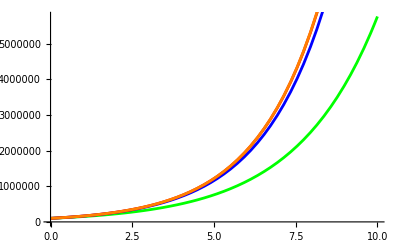

```mathematica
r = 0.5; (*urok*)
H0= 100000; (*vklad*)
f[doba_,t_] = H0*(Power[(1+r/doba), t*doba]);
(*ročne*)
n1 = 10;
p1 = Plot[f[1,x], {x, 0, n1}, PlotStyle->Green];
(*mesačne*)
n2= 12.08*n1;
p2 = Plot[f[12, x],{x, 0, n1}, PlotStyle -> Blue];
(*denne*)
n3= 365* n1;
p3= Plot[f[365, x], {x, 0, n1}, PlotStyle->Red];
(*spojité*)
p4 = Plot[H0*Power[E, r*x], {x, 0, n1}, PlotStyle->Orange];
Show[p1, p2, p3,p4]
```

```mathematica
(*3 uloha*)
```

```mathematica
ClearAll[X,Y,R,n,sn,v, an,r]
```

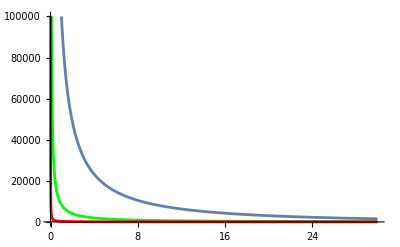

3133.63

1000.

```mathematica
X = 100000; (*cielova suma*)
R = 0.05;
m= 30; (*čas odkladania*)
Y[x_, n_, r_, type_]= (x/type)/((Power[(1+r), n]-1)/r);
v = 1/(1+r);
P31 = Plot[Y[X, x, R, 1], {x, 0, m}, PlotRange-> {0, X}]; (*graf znazorňuje množstvo peňazí, ktoré potrebujem pre určité roky, ak odkladám 3O rokov, musím odkladať 1505 eur ročne aby som mal nakonci 30 rokov 100 000 eur*)
P32 = Plot[Y[X, x, R, 12], {x, 0, m}, PlotRange-> {0, X}, PlotStyle->Green]; (*pri mesačnom urokovaní stači na 30 rokov odkladať 125 eur*)
P33 = Plot[Y[X, x, R, 365], {x, 0, m}, PlotRange-> {0, X}, PlotStyle->Red] ;(*pri dennom 4 eura*)
Show[P31, P32, P33]
```

```mathematica
ClearAll[X, n, r2, m, r1]
```

```mathematica
X=20000 ;  
n=20  ;    
r2=0.03   ;
m=35    ;
r1=0.04   ;
S_retirement=X*((1-(1+r2)**-n)/r2)
annual_savings=(S_retirement*r1)/((1+r1)**m-1)
```

666667. (1-1.03**(-20))

(0.04 S_retirement)/(-1+1.04**35)